```mathematica
zeta[x_,μ_,β_,gL_]=-1/β Log[1-β(μ Sin[x]/x+gL)];
```

```mathematica
CompactionC[x_,μ_,β_,gL_]=2/3(1-(1+x D[zeta[x,μ,β,gL], x])^2)//Simplify
```

2/3 (1-(x (-1+gL β)-x μ Cos[x]+(1+β) μ Sin[x])^2/(x (-1+gL β)+β μ Sin[x])^2)

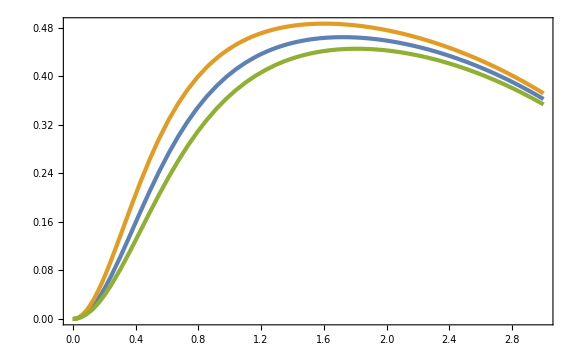

```mathematica
Plot[{CompactionC[x,0.3,3,0],CompactionC[x,0.3,3,0.01],CompactionC[x,0.3,3,-0.01]},{x,0,3}]
```

```mathematica
rmcond[x_,μ_,β_,gL_]=D[zeta[x,μ,β,gL], x]+x D[D[zeta[x,μ,β,gL], x], x]//Simplify
```

(μ (x β μ+(-1+x^2) (-1+gL β) Sin[x]-Cos[x] (x-gL x β+β μ Sin[x])))/(x (-1+gL β)+β μ Sin[x])^2

```mathematica
rmcond0[xm0_,μ_,β_]=(xm0-β μ Sin[xm0])^2 Normal[Series[rmcond[xm0+gL xm1,μ,β,gL],{gL,0,0}]]//Simplify
```

μ (xm0 β μ+Sin[xm0]-xm0^2 Sin[xm0]-Cos[xm0] (xm0+β μ Sin[xm0]))

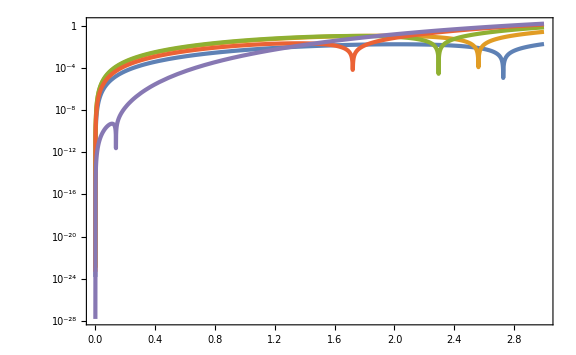

```mathematica
LogPlot[{Abs[rmcond0[xm0,10^-2,3]],Abs[rmcond0[xm0,1/10,3]],Abs[rmcond0[xm0,2/10,3]],Abs[rmcond0[xm0,3/10,3]],Abs[rmcond0[xm0,1/3-10^-6,3]]},{xm0,0,3},PlotRange->Full,WorkingPrecision->30]
```

```mathematica
xm03List=Table[{1/3-10^logdmu,xm0/.FindRoot[rmcond0[xm0,1/3-10^logdmu,3]==0,{xm0,3},WorkingPrecision->30]},{logdmu,-6,Log10[1/3],10^-2}];
```

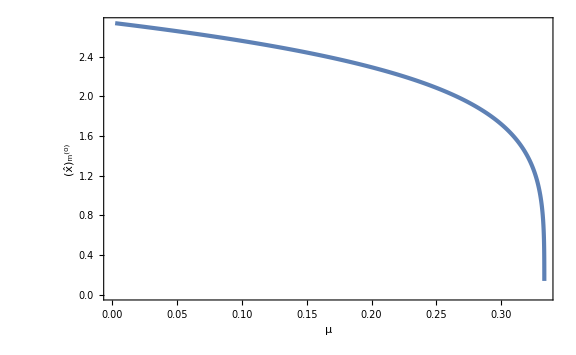

```mathematica
ListPlot[xm03List,PlotRange->Full,FrameLabel->{{Subscript[OverHat[x], "m"]^("(0)"),None},{μ,β==3}}]
```

```mathematica
xm03int[μ_]=Interpolation[xm03List][μ];
```

```mathematica
rmcond1[xm0_,xm1_,μ_,β_]=D[Normal[Series[rmcond[xm0+gL xm1,μ,β,gL],{gL,0,1}]], gL]//Simplify
```

1/(xm0-β μ Sin[xm0])^3 μ (-2 (-xm1+xm0 β+xm1 β μ Cos[xm0]) (-xm0 β μ+(-1+xm0^2) Sin[xm0]+Cos[xm0] (xm0+β μ Sin[xm0]))+(-xm0+β μ Sin[xm0]) (xm0 (xm0 xm1-β) Cos[xm0]+Sin[xm0] (xm0 xm1+β-xm0^2 β-2 xm1 β μ Sin[xm0])))

```mathematica
xm1sol[xm0_,μ_,β_]=xm1/.Solve[rmcond1[xm0,xm1,μ,β]==0,xm1][[1]]//Simplify
```

(β (β μ+3 xm0^2 β μ-2 xm0^2 Cos[xm0]+(-1+xm0^2) β μ Cos[2 xm0]+2 xm0 Sin[xm0]-2 xm0^3 Sin[xm0]-3 xm0 β μ Sin[2 xm0]))/(2 (xm0 Cos[xm0]-Sin[xm0]) (-2+xm0^2-2 β^2 μ^2+4 β μ Cos[xm0]+xm0 β μ Sin[xm0]))

```mathematica
Normal[Series[xm1sol[xm0,μ,3],{xm0,0,1}]]
```

(3 xm0)/(-1+3 μ)

InterpolatingFunction::dmval: Input value {6.80952×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

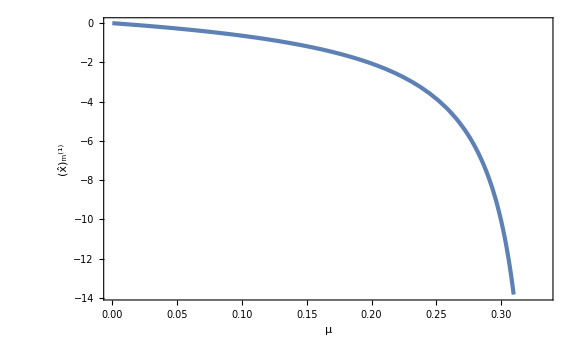

```mathematica
Plot[xm1sol[xm03int[μ],μ,3],{μ,0,1/3},FrameLabel->{{Subscript[OverHat[x], "m"]^("(1)"),None},{μ,β==3}}]
```

```mathematica
Cm0[xm0_,μ_,β_]=Normal[Series[CompactionC[xm0+gL xm1,μ,β,gL],{gL,0,0}]]//Simplify
```

2/3 (1-(xm0+xm0 μ Cos[xm0]-(1+β) μ Sin[xm0])^2/(xm0-β μ Sin[xm0])^2)

```mathematica
Cm1[xm0_,xm1_,μ_,β_]=D[Normal[Series[CompactionC[xm0+gL xm1,μ,β,gL],{gL,0,1}]], gL]//Simplify
```

1/(3 (xm0-β μ Sin[xm0])^3)4 μ (xm0+xm0 μ Cos[xm0]-(1+β) μ Sin[xm0]) (-xm0 xm1 β μ+((-1+xm0^2) xm1+xm0 β) Sin[xm0]+Cos[xm0] (xm0 (xm1-xm0 β)+xm1 β μ Sin[xm0]))

InterpolatingFunction::dmval: Input value {6.80952×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

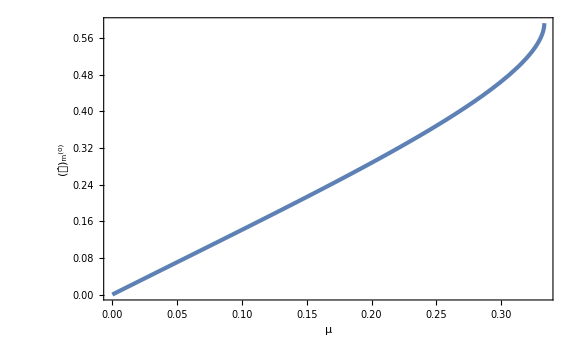

```mathematica
Plot[Cm0[xm03int[μ],μ,3],{μ,0,1/3},FrameLabel->{{Subscript[OverHat[𝒞], "m"]^("(0)"),None},{μ,β==3}}]
```

InterpolatingFunction::dmval: Input value {6.80952×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

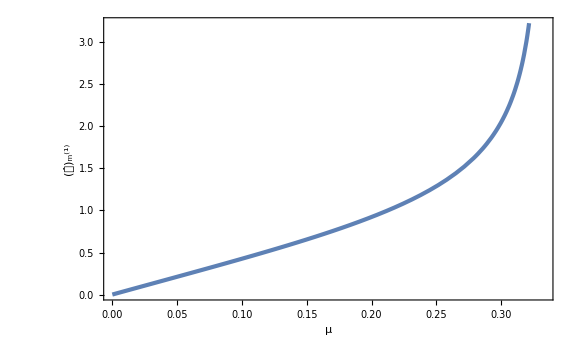

```mathematica
Plot[Cm1[xm03int[μ],xm1sol[xm03int[μ],μ,3],μ,3],{μ,0,1/3},FrameLabel->{{Subscript[OverHat[𝒞], "m"]^("(1)"),None},{μ,β==3}}]
```

```mathematica
qq[xm_,μ_,β_,gL_]=-1/4 xm^2 D[D[CompactionC[xm,μ,β,gL], xm], xm]/(CompactionC[xm,μ,β,gL](1-3/2 CompactionC[xm,μ,β,gL]))//Simplify
```

-((xm^2 (-(-1+gL β+β μ Cos[xm]+xm μ Sin[xm])^2 (xm (-1+gL β)+β μ Sin[xm])^2+μ (xm Cos[xm]+Sin[xm]-β Sin[xm]) (xm (-1+gL β)+β μ Sin[xm])^2 (xm-gL xm β+xm μ Cos[xm]-(1+β) μ Sin[xm])+4 (-1+gL β+β μ Cos[xm]) (-1+gL β+β μ Cos[xm]+xm μ Sin[xm]) (xm (-1+gL β)+β μ Sin[xm]) (xm (-1+gL β)-xm μ Cos[xm]+(1+β) μ Sin[xm])-3 (-1+gL β+β μ Cos[xm])^2 (xm (-1+gL β)-xm μ Cos[xm]+(1+β) μ Sin[xm])^2-β μ Sin[xm] (xm (-1+gL β)+β μ Sin[xm]) (xm (-1+gL β)-xm μ Cos[xm]+(1+β) μ Sin[xm])^2))/(2 (xm (-1+gL β)+β μ Sin[xm])^2 (xm (-1+gL β)-xm μ Cos[xm]+(1+β) μ Sin[xm])^2 (1-(xm (-1+gL β)-xm μ Cos[xm]+(1+β) μ Sin[xm])^2/(xm (-1+gL β)+β μ Sin[xm])^2)))

```mathematica
qq0[xm0_,μ_,β_]=Normal[Series[qq[xm0+gL xm1,μ,β,gL],{gL,0,0}]]//Simplify
```

-((xm0^2 (-(-1+β μ Cos[xm0]+xm0 μ Sin[xm0])^2 (xm0-β μ Sin[xm0])^2+μ (xm0 Cos[xm0]+Sin[xm0]-β Sin[xm0]) (xm0-β μ Sin[xm0])^2 (xm0+xm0 μ Cos[xm0]-(1+β) μ Sin[xm0])-3 (-1+β μ Cos[xm0])^2 (xm0+xm0 μ Cos[xm0]-(1+β) μ Sin[xm0])^2-β μ Sin[xm0] (-xm0+β μ Sin[xm0]) (xm0+xm0 μ Cos[xm0]-(1+β) μ Sin[xm0])^2+4 (-1+β μ Cos[xm0]) (-1+β μ Cos[xm0]+xm0 μ Sin[xm0]) (-xm0+β μ Sin[xm0]) (-xm0-xm0 μ Cos[xm0]+(1+β) μ Sin[xm0])))/(2 (xm0-β μ Sin[xm0])^2 (xm0+xm0 μ Cos[xm0]-(1+β) μ Sin[xm0])^2 (1-(xm0+xm0 μ Cos[xm0]-(1+β) μ Sin[xm0])^2/(xm0-β μ Sin[xm0])^2)))

```mathematica
qq1[xm0_,xm1_,μ_,β_]=D[Normal[Series[qq[xm0+gL xm1,μ,β,gL],{gL,0,1}]], gL]//Simplify
```

(xm0 ((8 (-(-1+β μ Cos[xm0]+xm0 μ Sin[xm0])^2 (xm0-β μ Sin[xm0])^2+μ (xm0 Cos[xm0]+Sin[xm0]-β Sin[xm0]) (xm0-β μ Sin[xm0])^2 (xm0+xm0 μ Cos[xm0]-(1+β) μ Sin[xm0])-3 (-1+β μ Cos[xm0])^2 (xm0+xm0 μ Cos[xm0]-(1+β) μ Sin[xm0])^2-β μ Sin[xm0] (-xm0+β μ Sin[xm0]) (xm0+xm0 μ Cos[xm0]-(1+β) μ Sin[xm0])^2+4 (-1+β μ Cos[xm0]) (-1+β μ Cos[xm0]+xm0 μ Sin[xm0]) (-xm0+β μ Sin[xm0]) (-xm0-xm0 μ Cos[xm0]+(1+β) μ Sin[xm0])) (xm0^3 xm1 (1+2 β) μ^2 Cos[xm0]^3+xm0^2 μ Cos[xm0]^2 (xm0 (xm1+2 xm0 β+3 xm1 β)+xm1 (-3+2 xm0^2-7 β-3 β^2) μ Sin[xm0])+xm0 Cos[xm0] (xm0^2 (-xm1+3 xm0 β)+xm0 (xm1 (-2+4 xm0^2-4 β)-xm0 β (4+3 β)) μ Sin[xm0]-xm1 (-3+4 xm0^2-5 β) (1+β) μ^2 Sin[xm0]^2)+Sin[xm0] (xm0^2 (xm1+xm0^2 xm1-3 xm0 β)-xm0 (-xm0 β (2+3 β)+xm1 (-1-β+2 xm0^2 (2+β))) μ Sin[xm0]+xm1 (-1-3 β-2 β^2+xm0^2 (2+4 β+β^2)) μ^2 Sin[xm0]^2)))/(μ (-xm0 Cos[xm0]+Sin[xm0])^2)-1/(xm0 Cos[xm0]-Sin[xm0])xm0 (xm0+xm0 μ Cos[xm0]-(1+β) μ Sin[xm0]) (2 xm0+xm0 μ Cos[xm0]-(1+2 β) μ Sin[xm0]) (-12 β μ-16 xm0 xm1 β μ-8 β^2 μ+16 xm0^2 β^2 μ+16 xm0 xm1 β^2 μ^3+(12 xm0^4 β+2 β^2 (3+2 β) μ^2-3 xm0^3 xm1 (4+3 β μ^2)+xm0^2 β (-24+16 β μ^2-9 β^2 μ^2)+xm0 xm1 (8-17 β μ^2+11 β^2 μ^2)) Cos[xm0]-4 β μ (-3-2 xm0^4+xm0^2 (6-4 β)-2 β+2 xm0 xm1 (1+2 β μ^2+β^2 μ^2)) Cos[2 xm0]+17 xm0 xm1 β μ^2 Cos[3 xm0]-3 xm0^3 xm1 β μ^2 Cos[3 xm0]-6 β^2 μ^2 Cos[3 xm0]+8 xm0^2 β^2 μ^2 Cos[3 xm0]+13 xm0 xm1 β^2 μ^2 Cos[3 xm0]-4 β^3 μ^2 Cos[3 xm0]+xm0^2 β^3 μ^2 Cos[3 xm0]-8 xm1 Sin[xm0]+4 xm0^2 xm1 Sin[xm0]+4 xm0^4 xm1 Sin[xm0]+24 xm0 β Sin[xm0]-12 xm0^3 β Sin[xm0]+21 xm1 β μ^2 Sin[xm0]-11 xm0^2 xm1 β μ^2 Sin[xm0]-15 xm0 β^2 μ^2 Sin[xm0]+9 xm0^3 β^2 μ^2 Sin[xm0]-3 xm1 β^2 μ^2 Sin[xm0]-9 xm0^2 xm1 β^2 μ^2 Sin[xm0]+7 xm0 β^3 μ^2 Sin[xm0]+8 xm0^4 xm1 μ Sin[2 xm0]+24 xm0 β μ Sin[2 xm0]-16 xm0^3 β μ Sin[2 xm0]+12 xm1 β μ Sin[2 xm0]+16 xm0^2 xm1 β μ Sin[2 xm0]-8 xm0 β^2 μ Sin[2 xm0]-4 xm1 β^2 μ^3 Sin[2 xm0]-8 xm0^2 xm1 β^2 μ^3 Sin[2 xm0]+4 xm1 β^3 μ^3 Sin[2 xm0]-7 xm1 β μ^2 Sin[3 xm0]+21 xm0^2 xm1 β μ^2 Sin[3 xm0]-11 xm0 β^2 μ^2 Sin[3 xm0]+xm0^3 β^2 μ^2 Sin[3 xm0]-7 xm1 β^2 μ^2 Sin[3 xm0]+3 xm0^2 xm1 β^2 μ^2 Sin[3 xm0]-5 xm0 β^3 μ^2 Sin[3 xm0]+2 xm1 β^2 μ^3 Sin[4 xm0])))/(8 (xm0+xm0 μ Cos[xm0]-(1+β) μ Sin[xm0])^3 (2 xm0+xm0 μ Cos[xm0]-(1+2 β) μ Sin[xm0])^2)

InterpolatingFunction::dmval: Input value {6.80952×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

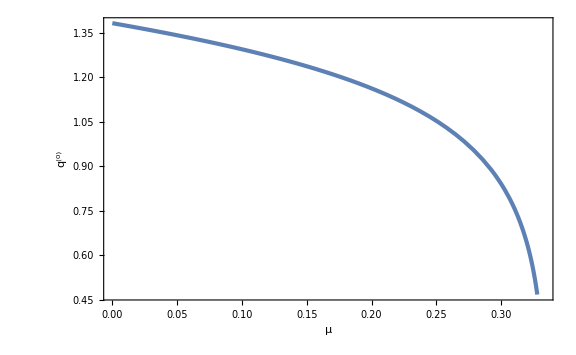

```mathematica
Plot[qq0[xm03int[μ],μ,3],{μ,0,1/3},FrameLabel->{{q^("(0)"),None},{μ,β==3}}]
```

InterpolatingFunction::dmval: Input value {6.80952×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

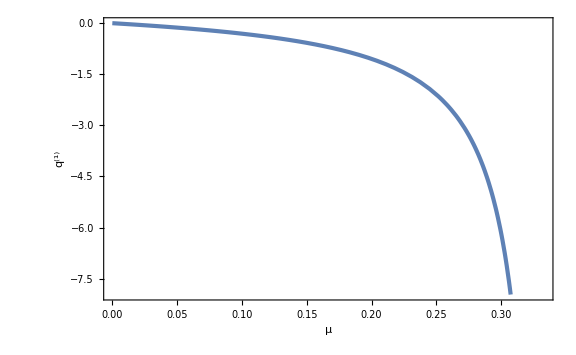

```mathematica
Plot[qq1[xm03int[μ],xm1sol[xm03int[μ],μ,3],μ,3],{μ,0,1/3},FrameLabel->{{q^("(1)"),None},{μ,β==3}}]
```